# Test Student-T vNDF null sample

## License

/*
 * Copyright (c) <2023> NVIDIA CORPORATION & AFFILIATES. All rights reserved.
 *
 * Licensed under the Apache License, Version 2.0 (the “License”);
 * you may not use this file except in compliance with the License.
 * You may obtain a copy of the License at
 *
 *     http://www.apache.org/licenses/LICENSE-2.0
 *
 * Unless required by applicable law or agreed to in writing, software
 * distributed under the License is distributed on an “AS IS” BASIS,
 * WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
 * See the License for the specific language governing permissions and
 * limitations under the License.
 */

```mathematica
Run["clang++ -I include test/NDFs/test_ST_vNDF.cpp -O3 -o test/NDFs/test_ST_vNDF"]
```

0

```mathematica
Run["clang++ -I include test/NDFs/test_ST_vNDF_null.cpp -O3 -o test/NDFs/test_ST_vNDF_null"]
```

0

```mathematica
roughness="0.8";
majorant=".6";
gamma="2.7";
thetai=".6";
phi="1.2";
```

```mathematica
ST`D[u_,α_,γ_]:=((1+(1-u^2)/(u^2 α^2 (-1+γ)))^-γ)/(π u^4 α^2)HeavisideTheta[u]
```

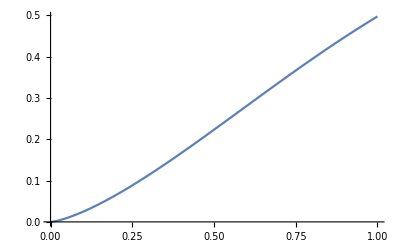

```mathematica
Plot[ST`D[u,0.8,2.7],{u,0,1}]
```

```mathematica
argstr=roughness<>" "<>majorant<>" "<>gamma<>" "<>thetai<>" "<>phi<>" 10000000 100 > test/NDFs/MC.txt"
```

0.8 .6 2.7 .6 1.2 10000000 100 > test/NDFs/MC.txt

```mathematica
Run["./test/NDFs/test_ST_vNDF_null "<>argstr]
```

0

```mathematica
check=Import["test/NDFs/MC.txt","Table"];
```

```mathematica
nullEval=check[[-100;;-1]];
nullSample=check[[2;;101]];
```

```mathematica
argstr=roughness<>" "<>roughness<>" "<>gamma<>" "<>thetai<>" "<>phi<>" 10000000 100 > test/NDFs/MC.txt"
```

0.8 0.8 2.7 .6 1.2 10000000 100 > test/NDFs/MC.txt

```mathematica
Run["./test/NDFs/test_ST_vNDF "<>argstr]
```

0

```mathematica
check=Import["test/NDFs/MC.txt","Table"];
```

```mathematica
imEval=check[[-100;;-1]];
imSample=check[[2;;101]];
```

```mathematica
b=.5/Max[Flatten[imEval]];
gamma=0.3;
```

```mathematica
{Image[(b Abs[nullEval])^gamma],Image[(b nullSample)^gamma],Image[(b Abs[imEval])^gamma],Image[(b imSample)^gamma],(Image[(b Abs[nullEval-nullSample])^gamma]),(Image[(b Abs[nullSample-imSample])^gamma])}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

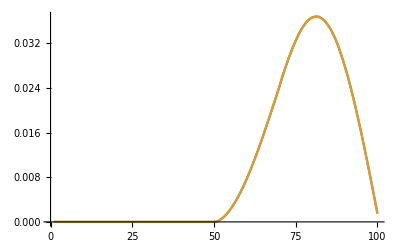

```mathematica
ListPlot[Total/@{Transpose[nullEval],Transpose[nullSample]},Joined->True,PlotRange->All]
```

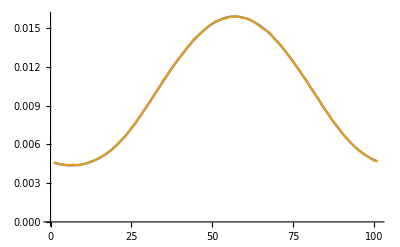

```mathematica
ListPlot[Total/@{nullEval,nullSample},Joined->True]
```